# Chapter 8 - Problem 2

The first excited state is the second node (zero) of the determinant of the transfer matrix. That means, this problem is very similar to Chapter 8 - Problem 1.

```mathematica
Clear["Global`*"]
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
e = 1.60217 * 10^-19;
nano = 1 * 10^-9;
```

We know the length of the well is 1 nm. We can also try to solve the problem when the constant external electric field is 0.5 V/nm before we solve the problem for an external electric field varying from 0.1 V/nm to 0.5 V/nm.

```mathematica
L = 1*nano;
voltspernano = 1/nano;
F = 0.5 * voltspernano;
```

We’re going to break parts of the transfer matrix into pieces to make it easier for us

```mathematica
a = ((2*m*e*F)/ℏ^2)^(1/3);
b = (-en * e)/(e*F);
```

so now we can begin to build the transfer matrix:

```mathematica
M11 = AiryAi[a*b];
M12 = AiryBi[a*b];
M21 = AiryAi[a*(b-L)];
M22 = AiryBi[a*(b-L)];
transfer = {{M11, M12},{M21, M22}};
MatrixForm[transfer]
```

(AiryAi[-4.7175 en] | AiryBi[-4.7175 en]
AiryAi[2.35875×10^9 (-1/1000000000-2.×10^-9 en)] | AiryBi[2.35875×10^9 (-1/1000000000-2.×10^-9 en)])

```mathematica
det = Det[transfer]
```

AiryAi[-4.7175 en] AiryBi[2.35875×10^9 (-1/1000000000-2.×10^-9 en)]-AiryAi[2.35875×10^9 (-1/1000000000-2.×10^-9 en)] AiryBi[-4.7175 en]

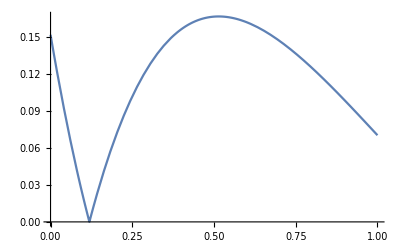

```mathematica
Plot[Abs[det],{en,0,1}](* we can see the first node from this plot, we have to see the second one*)
```

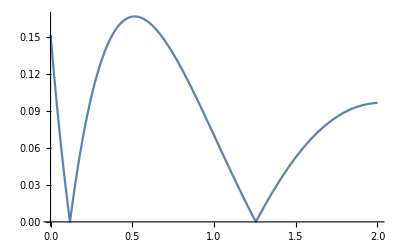

```mathematica
Plot[Abs[det],{en,0,2}] (* now we can see the second node, so let's find where it is*)
```

We can see that the second node (zero) occurs at around 1.25, so we can find use the FindRoot function

```mathematica
FindRoot[det == 0, {en,1.25}]
```

{en→1.25625}

#### Now we can redo the problem with an F that is varying from 0.1 V/nm and 0.5 V/nm

```mathematica
Clear["Global`*"]
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
e = 1.60217 * 10^-19;
nano = 1 * 10^-9;
voltspernano = 1/nano;
L = 1*nano;
a = ((2*m)/ℏ^2 * e *F)^(1/3);
b =(-en * e)/(e*F); 
m11 = AiryAi[a *b];
m12 = AiryBi[a*b];
m21 = AiryAi[a*(b-L)];
m22 = AiryBi[a * (b-L)];
det = m11 * m22 - m21* m12
```

-AiryAi[2.97184×10^6 (-1/1000000000-(1. en)/F) F^(1/3)] AiryBi[-(2.97184×10^6 en)/F^(2/3)]+AiryAi[-(2.97184×10^6 en)/F^(2/3)] AiryBi[2.97184×10^6 (-1/1000000000-(1. en)/F) F^(1/3)]

```mathematica
Table[FindRoot[det==0,{en,1.3}],{F,0.1*voltspernano, 0.5*voltspernano, 0.01*voltspernano}];
firstexcitedenergy = en/.%
```

{1.45421,1.44923,1.44425,1.43927,1.4343,1.42932,1.42435,1.41938,1.41441,1.40944,1.40447,1.39951,1.39454,1.38958,1.38462,1.37966,1.37471,1.36975,1.3648,1.35985,1.3549,1.34995,1.345,1.34006,1.33512,1.33017,1.32523,1.3203,1.31536,1.31042,1.30549,1.30056,1.29563,1.2907,1.28578,1.28085,1.27593,1.27101,1.26609,1.26117,1.25625}

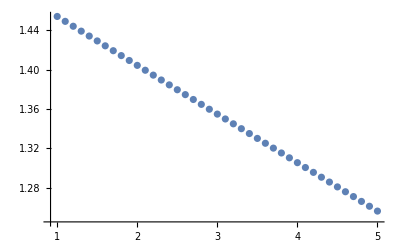

```mathematica
F = Table[F,{F,0.1*voltspernano, 0.5*voltspernano, 0.01*voltspernano}]; (* values of F in table form*)
ListPlot[Table[{F[[i]], firstexcitedenergy [[i]]}, {i,1,Length[F]}]]
```